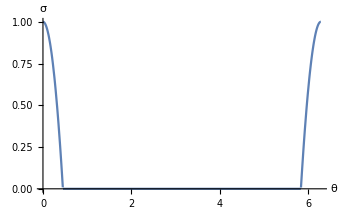

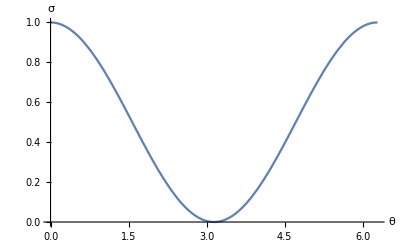

-Graphics3D-

-Graphics3D-

NIntegrate::inumr: The integrand 2.\ √b^2\ Cos[u]^2 + Sin[u]^2/-Sin[u]\ (-Cos[« 1 »]^2 - b\ Sin[u])/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + b\ Cos[u]\ (Cos[u] - b^2\ Sin[« 1 »]^2)/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + √Plus[« 2 »]^2/Plus[« 3 »]^2 + Plus[« 2 »]^2/Plus[« 3 »]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.\ √b^2\ Cos[u]^2 + Sin[u]^2/-Sin[u]\ (-Cos[« 1 »]^2 - b\ Sin[u])/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + b\ Cos[u]\ (Cos[u] - b^2\ Sin[« 1 »]^2)/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + √Plus[« 2 »]^2/Plus[« 3 »]^2 + Plus[« 2 »]^2/Plus[« 3 »]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{3.14159, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.\ √b^2\ Cos[u]^2 + Sin[u]^2/-Sin[u]\ (-Cos[« 1 »]^2 - b\ Sin[u])/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + b\ Cos[u]\ (Cos[u] - b^2\ Sin[« 1 »]^2)/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + √Plus[« 2 »]^2/Plus[« 3 »]^2 + Plus[« 2 »]^2/Plus[« 3 »]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.\ √b^2\ Cos[u]^2 + Sin[u]^2/-Sin[u]\ (-Cos[« 1 »]^2 - b\ Sin[u])/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + b\ Cos[u]\ (Cos[u] - b^2\ Sin[« 1 »]^2)/√Power[« 2 »]\ Power[« 2 »] + Sin[« 1 »]^2\ (1 + Cos[« 1 »]^2 + Power[« 2 »]\ Power[« 2 »]) + √Plus[« 2 »]^2/Plus[« 3 »]^2 + Plus[« 2 »]^2/Plus[« 3 »]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{3.14159, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
Clear[u,b]
gthetas[u_]:=Max[10*(Cos[u]-0.9),0]
gthetay[u_]:=((1+Cos[u])/2)
Plot[gthetas[u],{u,0,2Pi},AxesLabel->{θ,σ}]
Plot[gthetay[u],{u,0,2Pi},AxesLabel->{θ,σ}]
x[u_]:=Cos[u]
y[u_,b_]:=b*Sin[u]
r[u_,b_]:={Cos[u],b*Sin[u]}
w[u_,b_]:={-(x[u]^2+y[u,b])/(1+x[u]^2+y[u,b]^2),(x[u]-y[u,b]^2)/(1+x[u]^2+y[u,b]^2)}
w1[x_,y_]:={-(x^2+y)/(1+x^2+y^2),(x-y^2)/(1+x^2+y^2)}
v[u_,b_]:={-Sin[u],b*Cos[u]}
magv[u_,b_]:=√((Sin[u])^2+(b*Cos[u])^2)
magw[u_,b_]:=√(Dot[w[u,b],w[u,b]])
T[u_,b_]:=v[u,b]/magv[u,b]
sigmaY[u_,b_]:=.5*(magw[u,b]+Dot[w[u,b],T[u,b]])

Plot3D[sigmaY[u,b],{u,0,π},{b,0.01,2},AxesLabel->{u,b,σ}]
Plot3D[sigmaY[u,b],{u,π,2π},{b,0.01,2},AxesLabel->{u,b,σ}]

integrandparty[u_,b_]:=magv[u,b]/sigmaY[u,b]
t1[b_]:=NIntegrate[integrandparty[u,b],{u,0,π}]
t2[b_]:=NIntegrate[integrandparty[u,b],{u,π,2π}]
b1=b/.Last[NMinimize[t1[b],{b,0.01,2}]];
b2=b/.Last[NMinimize[t2[b],{b,0.01,2}]];
time1=First[NMinimize[t1[b],{b,0.01,2}]];
time2=First[NMinimize[t2[b],{b,0.01,2}]];
```

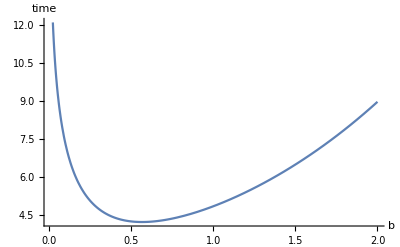

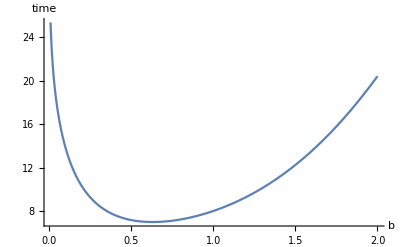

```mathematica
Plot[t1[b],{b,0.01,2},AxesLabel->{b ,time}]
Plot[t2[b],{b,0.01,2},AxesLabel->{b,time}]
```

```mathematica
p1=VectorPlot[w1[x,y],{x,-1,1},{y,-1,1}];
```

```mathematica
p2=ParametricPlot[{x[u],y[u,b1]},{u,0,Pi},PlotStyle->Red,AxesLabel->{Miles x10,Miles x10}];
```

```mathematica
p3=ParametricPlot[{x[u],y[u,b2]},{u,Pi,2Pi},PlotStyle->Red];
```

```mathematica
p4=Graphics[Circle[{0,0},0.25]];
arc1=NIntegrate[√((b1*Cos[u])^2+(-Sin[u])^2),{u,0,Pi}];
arc2=NIntegrate[√((b2*Cos[u])^2+(-Sin[u])^2),{u,Pi,2Pi}];
```

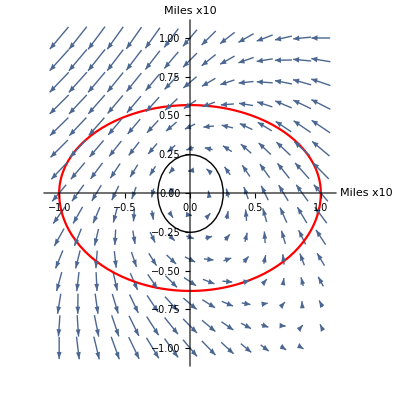

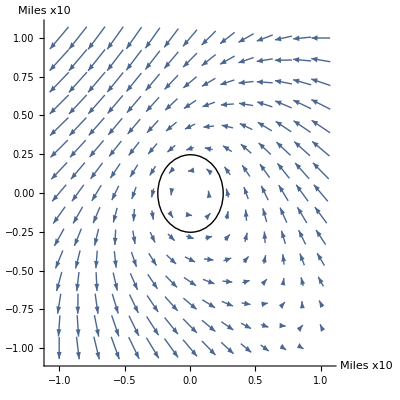

```mathematica
Show[p2,p1,p3,p4,PlotRange->All]
Show[p4,p1,Axes->True,PlotRange->All,AxesLabel->{Miles x10,Miles x10}]
```

-Graphics3D-

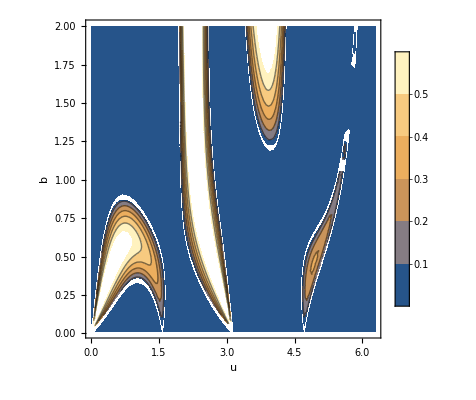

```mathematica
sigmaS[u_,b_]:=Max[10*(Dot[w[u,b],T[u,b]]-0.9*magw[u,b]),0]
Plot3D[sigmaS[u,b],{u,0,2Pi},{b,0.01,2},AxesLabel->{u,b,σ}]
ContourPlot[sigmaS[u,b],{u,0,2π},{b,0.01,2},FrameLabel->{u,b},PlotLegends->Automatic]
```

```mathematica
time1+time2
arc1+arc2
(arc1+arc2)/(time1+time2)
```

11.2323

5.10474

0.45447